```mathematica
Clear[n]
f[x_]:= Piecewise[{ {x, 0< x ≤ 1}, {2- x,1< x ≤ 2}}]
f2[x_]:= Piecewise[{ {f[x], x ≥ 0}, {f[-x], x < 0}}]
```

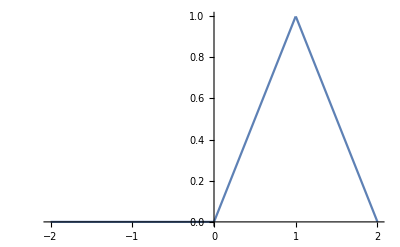

```mathematica
Plot[f[x], {x, -2, 2}]
```

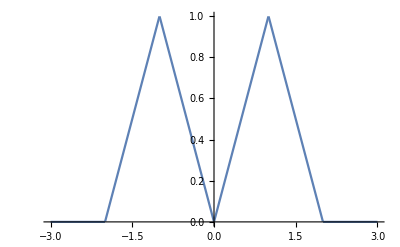

-Graphics-

```mathematica
Plot[f2[x], {x, -3, 3}]
```

```mathematica
Integrate[f2[x], {x, -2, 2}]
```

2

```mathematica
Integrate[x^2, {x, -1, 1}]
```

2/3

```mathematica
2/3
```

2/3

```mathematica
f3[x_]:= (2 - x) * Cos[(n*Pi*x)/2]
Integrate[f3[x], {x,a,b}]
```

(4 Cos[(a n π)/2]-4 Cos[(b n π)/2]+2 n π ((-2+a) Sin[(a n π)/2]-(-2+b) Sin[(b n π)/2]))/(n^2 π^2)

```mathematica
(4 Cos[(a n π)/2]-4 Cos[(b n π)/2]+2 n π ((-2+a) Sin[(a n π)/2]-(-2+b) Sin[(b n π)/2]))/(n^2 π^2)
```

(4 Cos[(a n π)/2]-4 Cos[(b n π)/2]+2 n π ((-2+a) Sin[(a n π)/2]-(-2+b) Sin[(b n π)/2]))/(n^2 π^2)

```mathematica
f4[x_] := x*Cos[(n*Pi*x)/2]
Integrate[f4[x], {x, 0, 1}]
```

(2 (-2+2 Cos[(n π)/2]+n π Sin[(n π)/2]))/(n^2 π^2)

```mathematica
(2 (-2+2 Cos[(n π)/2]+n π Sin[(n π)/2]))/(n^2 π^2)
Integrate[f3[x], {x, 1, 2}]
```

(2 (-2+2 Cos[(n π)/2]+n π Sin[(n π)/2]))/(n^2 π^2)

-(2 (-2 Cos[(n π)/2]+2 Cos[n π]+n π Sin[(n π)/2]))/(n^2 π^2)

```mathematica
Integrate[f3[x], {x, 1, 2}]
```

-(2 (-2 Cos[(n π)/2]+2 Cos[n π]+n π Sin[(n π)/2]))/(n^2 π^2)

```mathematica
Integrate[f4[x], {x, 0, 1}] + Integrate[f3[x], {x, 1, 2}]
```

(2 (-2+2 Cos[(n π)/2]+n π Sin[(n π)/2]))/(n^2 π^2)-(2 (-2 Cos[(n π)/2]+2 Cos[n π]+n π Sin[(n π)/2]))/(n^2 π^2)

```mathematica
Simplify[(2 (-2+2 Cos[(n π)/2]+n π Sin[(n π)/2]))/(n^2 π^2)-(2 (-2 Cos[(n π)/2]+2 Cos[n π]+n π Sin[(n π)/2]))/(n^2 π^2)]
```

(16 Cos[(n π)/2] Sin[(n π)/4]^2)/(n^2 π^2)

```mathematica
f5[x_]:= f[x] * Cos[(n*Pi*x)/2]
Integrate[f5[x], {x, 0, 2}]
```

(4 (-1+2 Cos[(n π)/2]-Cos[n π]))/(n^2 π^2)

```mathematica
(4 (-1+2 Cos[(n π)/2]-Cos[n π]))/(n^2 π^2)
```

(4 (-1+2 Cos[(n π)/2]-Cos[n π]))/(n^2 π^2)

```mathematica
F[x_,m_]:= .5 + Sum[( (4 (-1+2 Cos[(n π)/2]-Cos[n π]))/(n^2 π^2) )* Cos[(n*Pi*x)/2], {n, 1, m}]
```

```mathematica
Plot[{f[x],F[x, 3],F[x,10]} {x, 0, 2}, PlotLegends->"Expressions"]
```

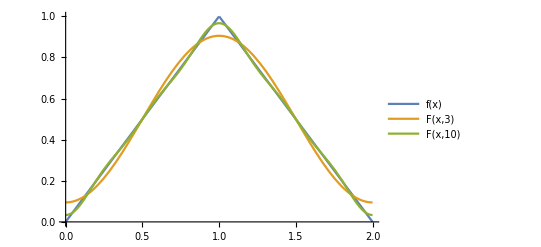

```mathematica
Plot[{f[x],F[x,3],F[x,10]} ,{x,0,2},PlotLegends->"Expressions"]
```